## Set Directory, Load in Files, etc.

```mathematica
(* Sets the Base directory, changing which files are easiest to acces. *)
dropBoxOn=FileNameJoin[{"Box Sync","Research","DataRuns"}];
If[SystemInformation["Kernel","OperatingSystem"]=="Unix",
(* The "data folder" is the folder in which ALL of the data you collect goes into *)
dataFolder=FileNameJoin[{"/","home","karl",dropBoxOn}]; ,(* Home coputer is Linux, so needs "/" at beginning *)
dataFolder=FileNameJoin[{"C:","Users","kahrendsen2",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"*)
];

(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
(* The "studyFolder" is the folder which contains all of the data related to one experimental questions i.e. "What is the relationship between these two variables?" *)
studyFolder=FileNameJoin[{dataFolder,"2018-12-14","data"}]
SetDirectory[studyFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=Length[directories],i>0,i--,
Print[i -> directories[[i]]];]
```

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2018-12-14\data

1→ExFn_60mTorr_90Ei

## Initialization Cells

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large,PlotStyle->{Automatic,20},LabelStyle->27,GridLines->Automatic];
SetOptions[ListPlot,BaseStyle->{FontSize->24},ImageSize->Large,PlotMarkers->{Automatic,20},LabelStyle->27,ImageSize->{960,600},GridLines->Automatic];
SetOptions[ListLogPlot,BaseStyle->{FontSize->24},ImageSize->Large,PlotMarkers->{Automatic,20},LabelStyle->27,ImageSize->{960,600},GridLines->Automatic];

nA=1*^-9;
plotLabel="Plot Label";
yAxisLabel="Y";
xAxisLabel="X";
ps={LabelStyle->18,PlotLabel->plotLabel,AxesLabel->{xAxisLabel,yAxisLabel}}

GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];

GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,rawFile[[k]][[1]]->joinedWithSpaces];
,
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];


headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
Placed
GaussianAnalyzer[files_,timeString_,dependentVariableString_]:=Module[{fitInfo, bothPlot, derivativePlot,entry,file,ps,header,data,energy,energyDiff,depVar,depVarDiff,energyOneRemoved,depVarDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,dataLabel1,dataLabel2,x1,y1,offset, new23,plot,derPlot,index},
index=GetIndexOfFilenameFromTimestamp[files,timeString];
file=files[[index]];
entry=<||>;

header=GetFileHeaderInfo[file];
data=GetFileDataset[file];
energy=Reverse[Normal[data[All,"SecondaryElectronEnergy"]]];
depVar=Reverse[Normal[data[All,dependentVariableString]]];
depVarDiff=Differences[depVar];
energyDiff=Differences[energy];
energyOneRemoved=Take[energy,{1,-2}];
depVarDer=depVarDiff/energyDiff;
plot=ListPlot[Transpose[{energy,depVar}],PlotLabel->dependentVariableString<>" vs. Energy: "<>timeString,FrameLabel->{"'Slow' Electron Energy (eV)",dependentVariableString},Frame->True];
derPlot=ListPlot[Transpose[{energyOneRemoved,depVarDer}],PlotLabel->dependentVariableString<>" Derivative\nvs. Energy: "<>timeString,FrameLabel->{"'Slow' Electron Energy (eV)","Derivative"},Frame->True];


plotTitle="Gaussian Analysis";

plotData=Transpose[{energy,depVar}];
plotData2=Transpose[{energyOneRemoved,depVarDer}];


(*
yAxisTitle="d(Counts)/d(Energy)";
xAxisTitle="Electron Energy (eV)";
*)
dataLabel1="Data";
dataLabel2="Derivative";

ps={ImageSize->Large, PlotLabel->plotTitle,AxesLabel->{"X","Y"}};

plotData=plotData2;
gaussModel[x_]=ampl Evaluate[PDF[NormalDistribution[m,σ],x]];
(*Find the position of the peak of the derivative data*)
maxDerPos=Position[depVarDer,Max[depVarDer]][[1]];
energyOfPeak=energyOneRemoved[[maxDerPos]][[1]];

fit=NonlinearModelFit[plotData,gaussModel[x],{ampl,{m,energyOfPeak},{σ,.9}},x];
model=Normal[fit];
pe=fit["BestFitParameters"]; (*Parameter Estimates*)
errors=fit["ParameterErrors"];

new23=m-(2*Sqrt[2Log[10]]σ)/2/.pe;
offset=23-new23;



x1=energyOfPeak-(3σ/.pe);
y1=.25*(ampl)/.pe;
fitInfo=StringForm["μ=``± ``\nσ=``±``",NumberForm[m/.pe,3],NumberForm[errors[[2]],1],NumberForm[σ/.pe,3],NumberForm[errors[[3]],1]];
(*Print[Show[{Plot[gaussModel[x]/.pe,{x,energyOfPeak-5,energyOfPeak+5},PlotRange->All,PlotLabel->"Gaussian Fit To Derivative\nof "<>dependentVariableString<>" Analysis: "<> timeString,Frame->True,FrameLabel->{"'Slow' Electron Energy (eV)","Derivative"}],
Graphics[Text[fitInfo,{x1,y1}],BaseStyle->15],
ListPlot[plotData,PlotLabel->"PLOT2"]}]];*)
bothPlot=ListPlot[{Legended[plotData,dataLabel2],Legended[plotData2,dataLabel1]}];
derivativePlot=ListPlot[Legended[plotData2,dataLabel2],ps];

AppendTo[entry,header];
AppendTo[entry,<|dependentVariableString<>"plot"->plot,"N2Offset"-> data[1,"N2Offset"],"filBias"-> data[1,"bias"],dependentVariableString<>"onsetEnergy"-> m/.pe,dependentVariableString<>"onsetWidth"->  σ/.pe,dependentVariableString<>"lowEnergySignal"-> depVar[[1]],dependentVariableString<>"highEnergySignal"-> depVar[[-1]]|>];
entry
];

ExcitationFunctionProcessor[files_,timeString_]:=Module[{file,ps,header,data,energy,energyDiff,current,currentDiff,energyOneRemoved,currentDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,x1,y1,return ,i},
return=<||>;
AppendTo[return,GaussianAnalyzer[files,timeString,"CountRate"]];
AppendTo[return,GaussianAnalyzer[files,timeString,"Current"]];
i=GetIndexOfFilenameFromTimestamp[files,timeString];
AppendTo[return,"stackedPlot"->StackedExFnPlot[files[[i]] ] ];
return
];

GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];

GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"-> "",":"->""}]->joinedWithSpaces];
,
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"->"",":"->""}]->rawFile[[k]][[2]]];
];
k++;
];
association
];

StackedExFnPlot[fileName_]:=Module[{
fd (*fileDataset*),
fh(*fileHeaderInfo*),
scale(*the magnitude of the faraday cup current *),
temp(*The temperature of the reservoir (mislabeled as the target)*),
pN2(*The pressure on the collision cell convectron gauge*),
data1,data2,
totHe,counts,curr,
paddingx,paddingy,padding, options, spacing,
countsAndCurrent
},
fd=GetFileDataset[fileName];
fh=GetFileHeaderInfo[fileName];
scale=fh["MagnitudeOfCurrent(*10^-X)"];
temp=fh["CellTemp(Targ)"];
pN2=fh["CVGauge(N2)(Torr)"];
data1=fd[All,{"TotalHeOffset","CountRate"}];
{totHe,counts}=Transpose[Normal[data1[Values]]];
data1=Transpose[{totHe*(-1),counts}];
data2=fd[All,{"TotalHeOffset","Current"}];
{totHe,curr}=Transpose[Normal[data2[Values]]];
data2=Transpose[{totHe*(-1),curr*10^-scale/nA}];

paddingx=120;
paddingy=100;
padding={{paddingx,0},{paddingy,30}};
options={ImagePadding->padding,Frame->True};
spacing={0,-150};
GraphicsGrid[{{Show[ListLogPlot[data1,FrameTicks->{None,Automatic},options,FrameLabel->{None,"Count Rate (Hz)"},PlotRange->{Automatic,{50,5500}},GridLines->Automatic],Graphics[Text["temp="<>ToString[temp]<>"  BGP="<>ToString[pN2]<>"\nbias="<>ToString[fd[All,"bias"][[1]]]<>" N2Off="<>ToString[fd[All,"N2Offset"][[1]]],{Center,Top},{0,2}],BaseStyle->15]]},{ListPlot[data2,options,FrameLabel-> {"He Potential","Current (nA)"}]}},Spacings->spacing]
];

TwoAxisListPlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},
(*Graphs the data for both sets of plots *)
{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];
(*Pulls the ranges from the plots *)
{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};
(*Grabs where each of the tick marks are in the f plot *)
fticks=N@FindDivisions[frange,5];
(*Finds what tick marks the G plot has at the fPlot Range.*)
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

{LabelStyle→18,PlotLabel→Plot Label,AxesLabel→{X,Y}}

Placed

ExFn Stitching

## 3mTorr N2, 0 mTorr Rb

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\2018-07-31_excitationFunctionStudy\data\3mTorrN2_0mTorrRb

{EX2018-07-31_111011.dat,EX2018-07-31_112227.dat,EX2018-07-31_112646.dat}

<|Filename→/home/pi/RbData/2018-07-31/EX2018-07-31_112646.dat,USB1208->HP3617Aconversion→0.06214,FilamentBias→-129.3,NumberOfSecondsPerCountMeasurement→1,Comments→1.6 mTorr BGP, 0-60,IonGauge(Torr)→0.0238,CVGauge(N2)(Torr)→0.00164,CVGauge(He)(Torr)→0.00121,CurrTemp(Res)→57.4,SetTemp(Res)→0.,CurrTemp(Targ)→60.1,SetTemp(Targ)→47.2,MagnitudeOfCurrent(*10^-X)→8|>

41.1

2.6

-129.3

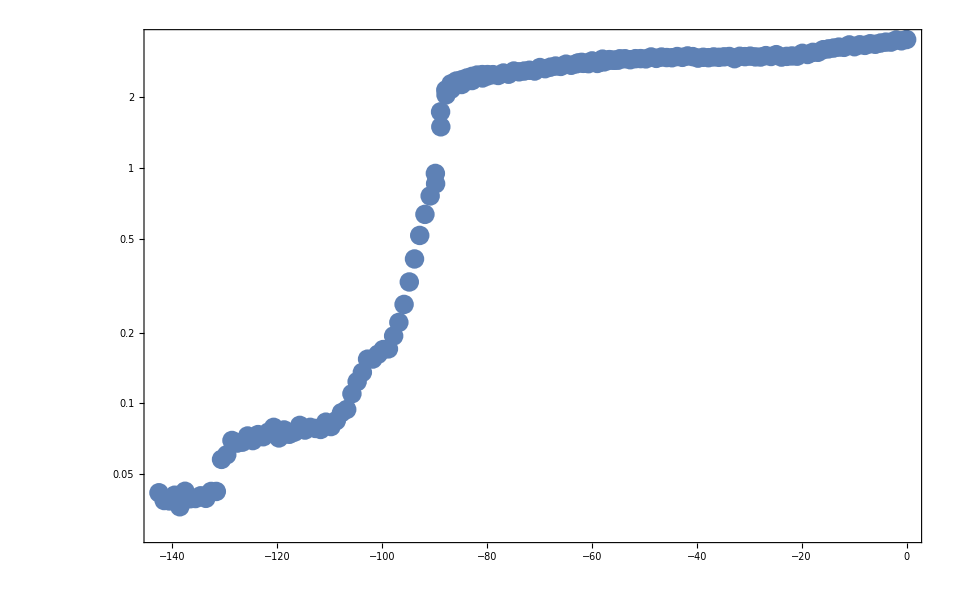

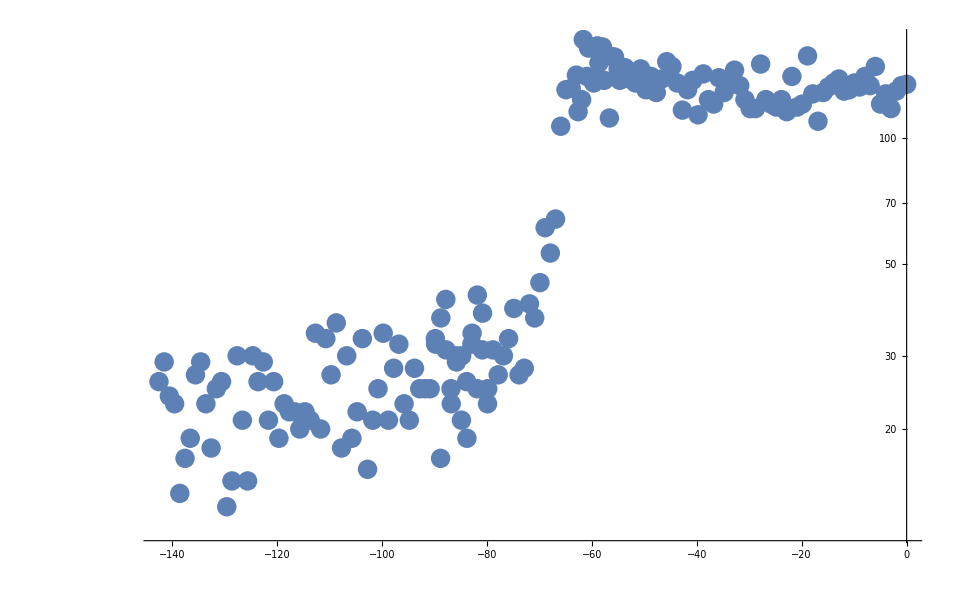

```mathematica
Clear[allDat];
SetDirectory["3mTorrN2_0mTorrRb"]
files=FileNames["EX*.dat"]
For[i=1,i≤Length[files],i++,
header=GetFileHeaderInfo[files[[i]]];
magnitude=header["MagnitudeOfCurrent(*10^-X)"];
dat=GetFileDataset[files[[i]]];
newDat=dat[All,<|#,"Current(nA)"-> #Current*10^(-magnitude+9)|>&];
If[i==1,allDat=newDat,allDat=Join[allDat,newDat]];
];
header
n2Offset=dat[All,"N2Offset"][[1]]
sweep=dat[All,"N2Sweep"][[1]]
filBias=dat[All,"bias"][[1]]
data1current=allDat[All,{"TotalHeOffset","Current(nA)"}];
data1count=allDat[All,{"TotalHeOffset","CountRate"}];
plot1current=ListLogPlot[allDat[All,{"TotalHeOffset","Current(nA)"}],PlotRange->Full,GridLines->Automatic,Frame->True,Ticks->Automatic]
plot1count=ListLogPlot[allDat[All,{"TotalHeOffset","CountRate"}]]
ResetDirectory[];
```

```mathematica
dat
```

Dataset[<>]

## Functionizing the above behavior

```mathematica
(* Take input of folder name, output stitched data and graphs of excitation functions. *)
```

```mathematica
CombineExcitationFunctions[folderName_]:=Module[{constantsFromDataToInclude,constantsFromHeaderToInclude,i,files,header, magnitude, dat, newDat, allDat,currentData,countData,currentPlot,countPlot,output},
output=<||>;
SetDirectory[folderName];
Print[FileNames["EX*.dat"]];
files=FileNames["EX*.dat"];
For[i=1,i≤Length[files],i++,
header=GetFileHeaderInfo[files[[i]]];
magnitude=header["MagnitudeOfCurrent(*10^-X)"];
dat=GetFileDataset[files[[i]]];
newDat=dat[All,<|#,"Current(nA)"-> #Current*10^(-magnitude+9)|>&];
If[i==1,allDat=newDat,allDat=Join[allDat,newDat]];
];
constantsFromHeaderToInclude={"CVGauge(N2)(Torr)","CurrTemp(Res)","CurrTemp(Targ)"};
For[i=1,i≤Length[constantsFromHeaderToInclude],i++,
AppendTo[output,constantsFromHeaderToInclude[[i]]->header[constantsFromHeaderToInclude[[i]]]];
];
constantsFromDataToInclude={"N2Offset","N2Sweep","bias"};
For[i=1,i≤Length[constantsFromDataToInclude],i++,
AppendTo[output,constantsFromDataToInclude[[i]]->dat[All,constantsFromDataToInclude[[i]]][[1]]];
];
sweep=dat[All,"N2Sweep"][[1]];
filBias=dat[All,"bias"][[1]];
currentData=allDat[All,{"TotalHeOffset","Current(nA)"}];
AppendTo[output,"currentData"->currentData];
countData=allDat[All,{"TotalHeOffset","CountRate"}];
AppendTo[output,"countData"->countData];
currentPlot=ListLogPlot[allDat[All,{"TotalHeOffset","Current(nA)"}],PlotRange->Full,GridLines->Automatic,Frame->True,FrameLabel->{"TotalHeOffset","Current(nA)"},Ticks->Automatic];
AppendTo[output,"currentPlot"->currentPlot];
countPlot=ListLogPlot[allDat[All,{"TotalHeOffset","CountRate"}]];
AppendTo[output,"countPlot"->countPlot];
ResetDirectory[];
output
];
```

## Testing the Function

```mathematica
Dataset[CombineExcitationFunctions["0mTorrN2_0mTorrRb"]]
```

{EX2018-07-31_151922.dat,EX2018-07-31_152155.dat,EX2018-07-31_152927.dat}

Dataset[<>]

## Loading in all the data

```mathematica
folderNames={"3mTorrN2_0mTorrRb","50mTorrN2_2evEi_0mTorrRb","50mTorrN2_50eVEi_0mTorrRb","50mTorrN2_100eVEi_0mTorrRb","1mTorrN2_2eVEi_0mTorrRb","1mTorrN2_50eVEi_0mTorrRb","1mTorrN2_100eVEi_0mTorrRb","130mTorrN2_100eVEi_0mTorrRb","130mTorrN2_50eVEi_0mTorrRb","130mTorrN2_2eVEi_0mTorrRb"};
Length[folderNames]
results=<||>;
For[i=1,i≤Length[folderNames],i++,
AppendTo[results,folderNames[[i]]->CombineExcitationFunctions[folderNames[[i]]]];
];
Dataset[results];
```

10

{EX2018-07-31_111011.dat,EX2018-07-31_112227.dat,EX2018-07-31_112646.dat}

{EX2018-07-31_221233.dat,EX2018-07-31_221527.dat,EX2018-07-31_221900.dat,EX2018-07-31_222222.dat}

{EX2018-07-31_233640.dat,EX2018-07-31_234246.dat,EX2018-07-31_234807.dat,EX2018-07-31_235007.dat}

{EX2018-07-31_225317.dat,EX2018-07-31_225849.dat,EX2018-07-31_230054.dat,EX2018-07-31_230428.dat}

{EX2018-08-01_121158.dat,EX2018-08-01_121456.dat,EX2018-08-01_121842.dat,EX2018-08-01_121956.dat}

{EX2018-08-01_112214.dat,EX2018-08-01_112512.dat,EX2018-08-01_112821.dat,EX2018-08-01_113040.dat}

{EX2018-08-01_133110.dat,EX2018-08-01_133703.dat,EX2018-08-01_133957.dat}

{EX2018-08-01_150415.dat,EX2018-08-01_150634.dat,EX2018-08-01_150923.dat}

{EX2018-08-01_154736.dat,EX2018-08-01_155023.dat,EX2018-08-01_155325.dat}

{EX2018-08-01_175658.dat,EX2018-08-01_180038.dat,EX2018-08-01_180318.dat,EX2018-08-01_180553.dat}

## Playing around with the dataset

{{-140,0},{0.005,150}}

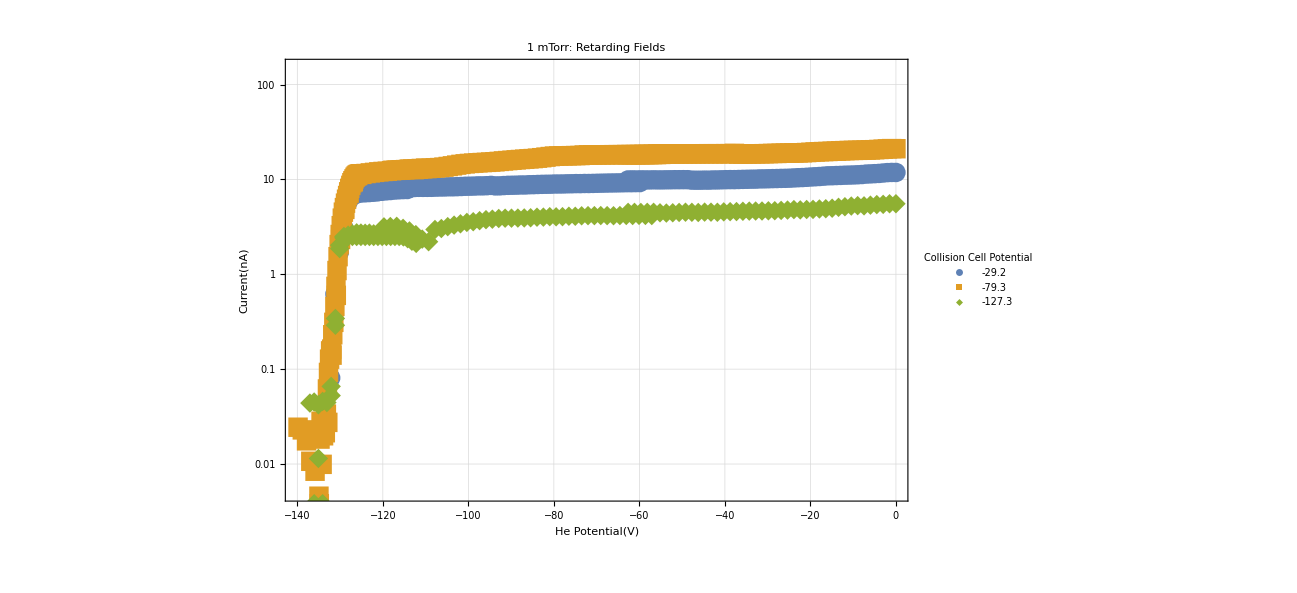

```mathematica
dataset=Dataset[results];
selectedDataset=Select[dataset,#["CVGauge(N2)(Torr)"]< .001&];
simplifiedDataset=selectedDataset[All,{"currentData","N2Offset","bias"}];
orderedDataset=simplifiedDataset[SortBy[-#["N2Offset"]&]];
plotRange={{-140,0},{.005,150}}
legendLabels={};
For[i=1,i≤Length[orderedDataset],i++,
AppendTo[legendLabels,Normal[orderedDataset[Values,"N2Offset"]][[i]]+Normal[orderedDataset[Values,"bias"]][[i]]];
];
plotData={};
For[i=1,i≤Length[orderedDataset],i++,
AppendTo[plotData,Normal[orderedDataset[Values,"currentData"]][[i]]];
];
ListLogPlot[plotData,PlotRange->plotRange,PlotLegends-> PointLegend[legendLabels,LegendLabel-> "Collision\nCell Potential"],Frame->True,FrameLabel-> {"He Potential(V)","Current(nA)"},PlotLabel->"1 mTorr: Retarding Fields"]
```

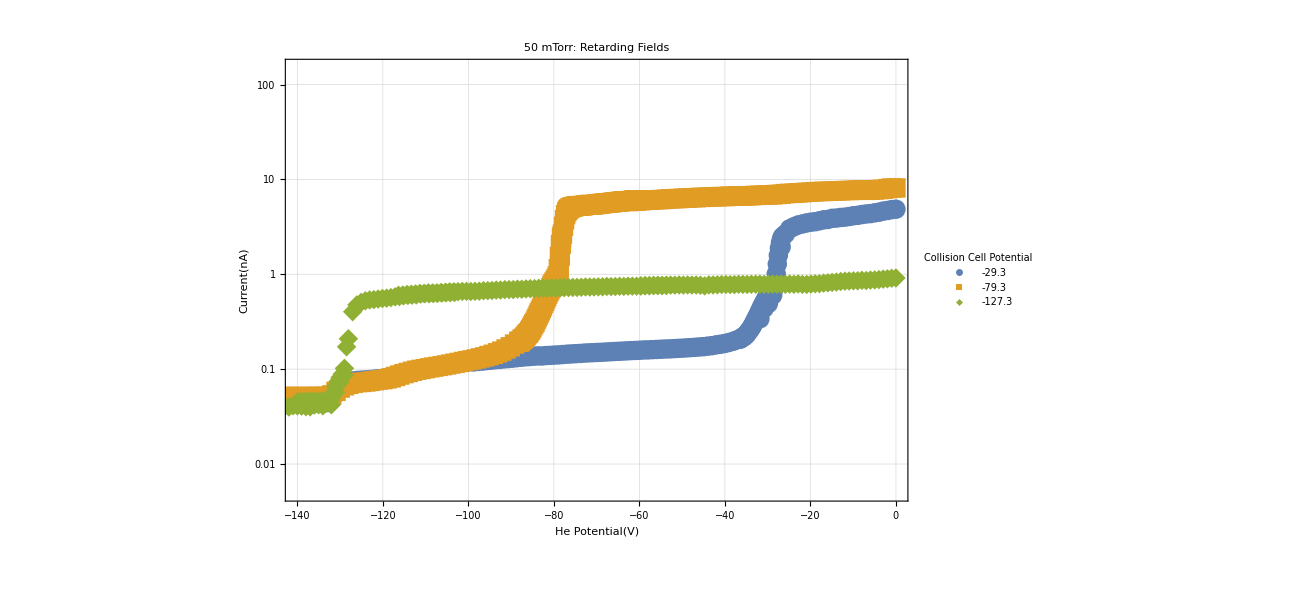

```mathematica
dataset=Dataset[results];
selectedDataset=Select[dataset,#["CVGauge(N2)(Torr)"]> .05&&#["CVGauge(N2)(Torr)"]< .07&];
simplifiedDataset=selectedDataset[All,{"currentData","N2Offset","bias"}];
orderedDataset=simplifiedDataset[SortBy[-#["N2Offset"]&]];
legendLabels={};
For[i=1,i≤Length[orderedDataset],i++,
AppendTo[legendLabels,Normal[orderedDataset[Values,"N2Offset"]][[i]]+Normal[orderedDataset[Values,"bias"]][[i]]];
];
plotData={};

For[i=1,i≤Length[orderedDataset],i++,
AppendTo[plotData,Normal[orderedDataset[Values,"currentData"]][[i]]];
];
ListLogPlot[plotData,PlotRange->plotRange,PlotLegends-> PointLegend[legendLabels,LegendLabel-> "Collision\nCell Potential"],Frame->True,FrameLabel-> {"He Potential(V)","Current(nA)"},PlotLabel->"50 mTorr: Retarding Fields"]
```

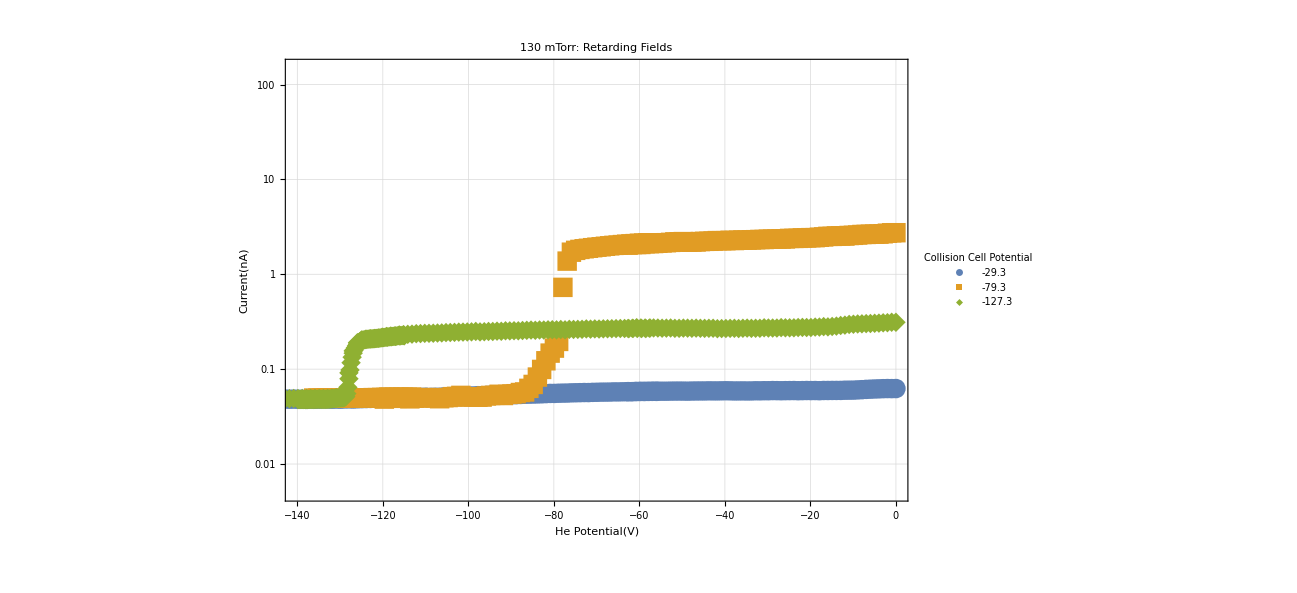

```mathematica
dataset=Dataset[results];
selectedDataset=Select[dataset,#["CVGauge(N2)(Torr)"]>.07&];
simplifiedDataset=selectedDataset[All,{"currentData","N2Offset","bias"}];
orderedDataset=simplifiedDataset[SortBy[-#["N2Offset"]&]];
legendLabels={};
For[i=1,i≤Length[orderedDataset],i++,
AppendTo[legendLabels,Normal[orderedDataset[Values,"N2Offset"]][[i]]+Normal[orderedDataset[Values,"bias"]][[i]]];
];
plotData={};

For[i=1,i≤Length[orderedDataset],i++,
AppendTo[plotData,Normal[orderedDataset[Values,"currentData"]][[i]]];
];
ListLogPlot[plotData,PlotRange->plotRange,PlotLegends-> PointLegend[legendLabels,LegendLabel-> "Collision\nCell Potential"],Frame->True,FrameLabel-> {"He Potential(V)","Current(nA)"},PlotLabel->"130 mTorr: Retarding Fields"]
```

Dr. Gay asked for a couple more runs, those are graphed here.

## Loading in all the data

```mathematica
folderNames={"130mTorrN2_80eVEi_0mTorrRb","130mTorrN2_61eVEi_0mTorrRb","130mTorrN2_57eVEi_0mTorrRb","130mTorrN2_50eVEi_0mTorrRb_08-03","130mTorrN2_23eVEi_0mTorrRb","130mTorrN2_5eVEi_0mTorrRb","130mTorrN2_2eVEi_0mTorrRb_08-03"};
Length[folderNames]
results=<||>;
For[i=1,i≤Length[folderNames],i++,
AppendTo[results,folderNames[[i]]->CombineExcitationFunctions[folderNames[[i]]]];
];
Dataset[results];
```

7

{EX2018-08-03_140702.dat,EX2018-08-03_140942.dat,EX2018-08-03_141256.dat}

{EX2018-08-03_152044.dat,EX2018-08-03_152303.dat,EX2018-08-03_152447.dat}

{EX2018-08-03_144800.dat,EX2018-08-03_145428.dat,EX2018-08-03_145523.dat,EX2018-08-03_145658.dat}

{EX2018-08-03_132528.dat,EX2018-08-03_132747.dat,EX2018-08-03_133020.dat}

{EX2018-08-03_120746.dat,EX2018-08-03_121104.dat,EX2018-08-03_130519.dat}

{EX2018-08-03_113029.dat,EX2018-08-03_114012.dat,EX2018-08-03_114730.dat,EX2018-08-03_114913.dat}

{EX2018-08-03_110540.dat,EX2018-08-03_111009.dat,EX2018-08-03_111406.dat,EX2018-08-03_111539.dat}

## Dr. Gay’s Requested Data

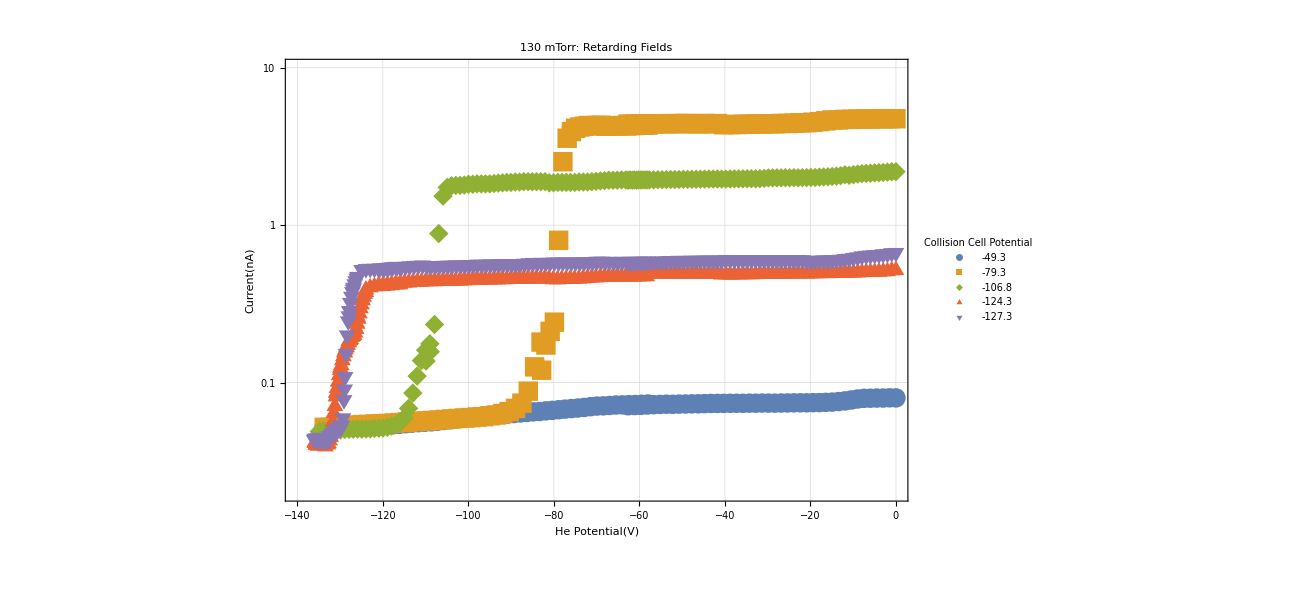

```mathematica
dataset=Dataset[results];
selectedDataset=Select[dataset,#["CVGauge(N2)(Torr)"]>.07&];
simplifiedDataset=selectedDataset[All,{"currentData","N2Offset","bias"}];
orderedDataset=simplifiedDataset[SortBy[-#["N2Offset"]&]];
plotRange={{-140,0},{.02,10}};
legendLabels={};
For[i=1,i≤Length[orderedDataset],i++,
AppendTo[legendLabels,Normal[orderedDataset[Values,"N2Offset"]][[i]]+Normal[orderedDataset[Values,"bias"]][[i]]];
];
plotData={};
For[i=1,i≤Length[orderedDataset],i++,
AppendTo[plotData,Normal[orderedDataset[Values,"currentData"]][[i]]];
];
ListLogPlot[plotData[[{1,4,5,6,7}]],PlotRange->plotRange,PlotLegends-> PointLegend[legendLabels[[{1,4,5,6,7}]],LegendLabel-> "Collision\nCell Potential"],Frame->True,FrameLabel-> {"He Potential(V)","Current(nA)"},PlotLabel->"130 mTorr: Retarding Fields"]
```

## Additional Data

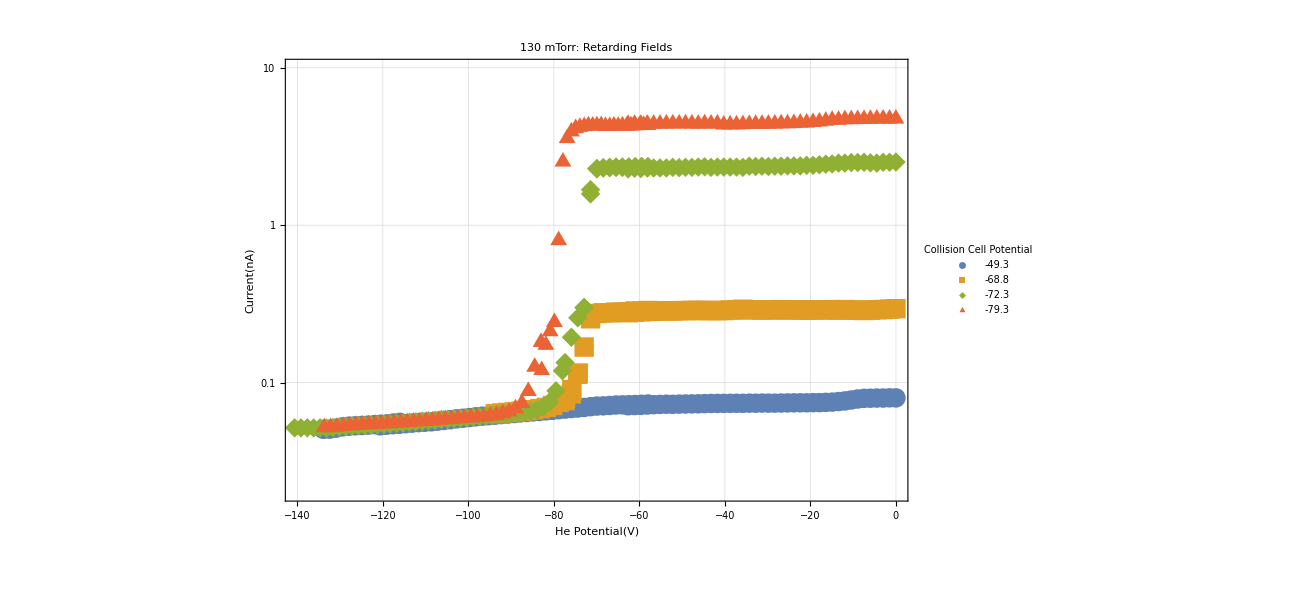

```mathematica
dataset=Dataset[results];
selectedDataset=Select[dataset,#["CVGauge(N2)(Torr)"]>.07&];
simplifiedDataset=selectedDataset[All,{"currentData","N2Offset","bias"}];
orderedDataset=simplifiedDataset[SortBy[-#["N2Offset"]&]];
plotRange={{-140,0},{.02,10}};
legendLabels={};
For[i=1,i≤Length[orderedDataset],i++,
AppendTo[legendLabels,Normal[orderedDataset[Values,"N2Offset"]][[i]]+Normal[orderedDataset[Values,"bias"]][[i]]];
];
plotData={};
For[i=1,i≤Length[orderedDataset],i++,
AppendTo[plotData,Normal[orderedDataset[Values,"currentData"]][[i]]];
];
ListLogPlot[plotData[[{1,2,3,4}]],PlotRange->plotRange,PlotLegends-> PointLegend[legendLabels[[{1,2,3,4}]],LegendLabel-> "Collision\nCell Potential"],Frame->True,FrameLabel-> {"He Potential(V)","Current(nA)"},PlotLabel->"130 mTorr: Retarding Fields"]
```

## Recreating Pirbhai’s PRARC

0.667364

{{80.,0.080018},{60.5,0.294715},{57.,2.52},{50.,4.75162},{22.5,2.18788},{5.,0.517526},{2.,0.667364}}

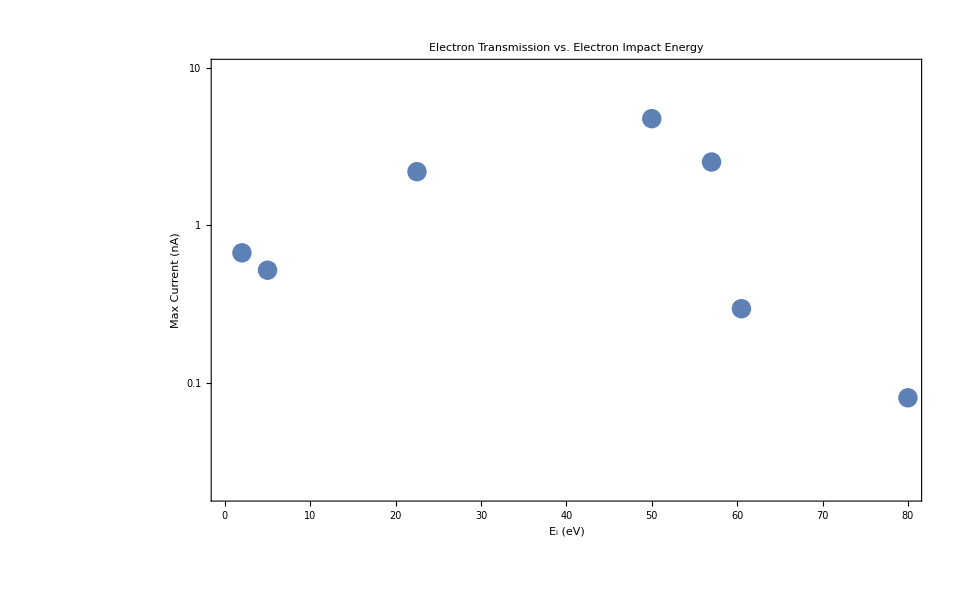

```mathematica
dataset=Dataset[results];
selectedDataset=Select[dataset,#["CVGauge(N2)(Torr)"]>.07&];
simplifiedDataset=selectedDataset[All,{"currentData","N2Offset","bias"}];
orderedDataset=simplifiedDataset[SortBy[-#["N2Offset"]&]];
plotRange={Automatic,{.02,10}};
collisionEnergy={};
For[i=1,i≤Length[orderedDataset],i++,
AppendTo[collisionEnergy,Normal[orderedDataset[Values,"N2Offset"]][[i]]];
];
plotData={};
For[i=1,i≤Length[legendLabels],i++,
ordPairs=Normal[orderedDataset[Values,"currentData"]][[i]];
maxCurrent=Max[Transpose[ordPairs][[2]]];
AppendTo[plotData,{collisionEnergy[[i]],maxCurrent}];
];
maxCurrent
plotData

ListLogPlot[plotData,PlotRange->plotRange,Frame->True,FrameLabel-> {"E_i (eV)","Max Current (nA)"},PlotLabel->"Electron Transmission vs. Electron Impact Energy"]
```

## Generate a single graph from a full scan.

1

{EX2018-12-14_154402.dat,EX2018-12-14_155453.dat,EX2018-12-14_160517.dat}

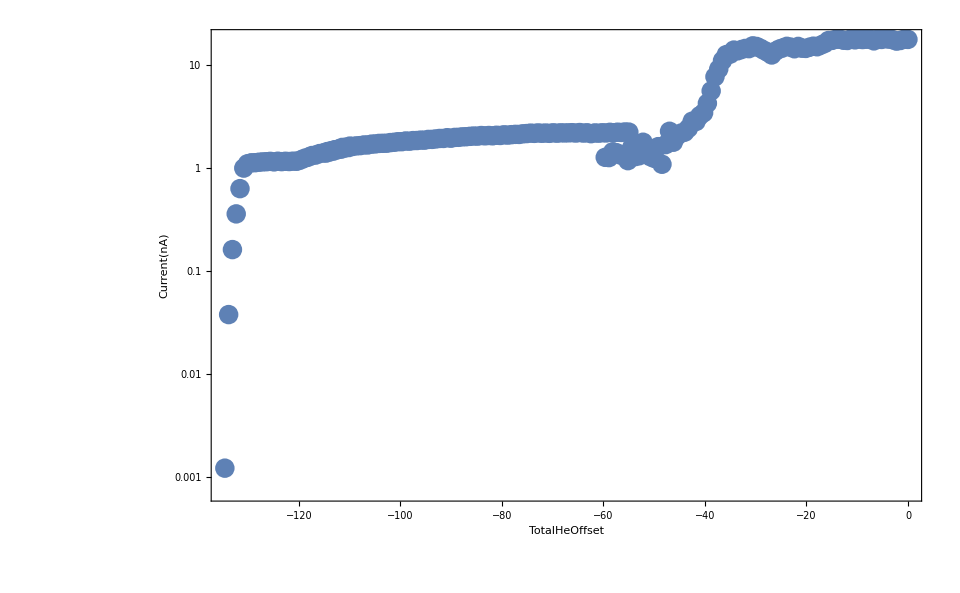

Part::partw: Part {1,4,5,6,7} of {} does not exist.

ListLogPlot::lpn: {}⟦{1,4,5,6,7}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

ListLogPlot[{}⟦{1,4,5,6,7}⟧,PlotRange→{{-140,0},{0.02,10}},PlotLegends→PointLegend[{}⟦{1,4,5,6,7}⟧,LegendLabel→Collision
Cell Potential],Frame→True,FrameLabel→{He Potential(V),Current(nA)},PlotLabel→130 mTorr: Retarding Fields]

```mathematica
folderNames={"ExFn_60mTorr_90Ei"};
Length[folderNames]
results=<||>;
For[i=1,i≤Length[folderNames],i++,
AppendTo[results,folderNames[[i]]->CombineExcitationFunctions[folderNames[[i]]]];
];
Dataset[results][[1]]["currentPlot"]
dataset=Dataset[results];
selectedDataset=Select[dataset,#["CVGauge(N2)(Torr)"]>.07&];
simplifiedDataset=selectedDataset[All,{"currentData","N2Offset","bias"}];
orderedDataset=simplifiedDataset[SortBy[-#["N2Offset"]&]];
plotRange={{-140,0},{.02,10}};
legendLabels={};
For[i=1,i≤Length[orderedDataset],i++,
AppendTo[legendLabels,Normal[orderedDataset[Values,"N2Offset"]][[i]]+Normal[orderedDataset[Values,"bias"]][[i]]];
];
plotData={};
For[i=1,i≤Length[orderedDataset],i++,
AppendTo[plotData,Normal[orderedDataset[Values,"currentData"]][[i]]];
];
ListLogPlot[plotData[[{1,4,5,6,7}]],PlotRange->plotRange,PlotLegends-> PointLegend[legendLabels[[{1,4,5,6,7}]],LegendLabel-> "Collision\nCell Potential"],Frame->True,FrameLabel-> {"He Potential(V)","Current(nA)"},PlotLabel->"130 mTorr: Retarding Fields"]
```